```mathematica
-Graphics-;
q=1.6×10^-19;
k=1.36×10^-23;
n=1.752;
Is=2.52*10^-9;
Rs=0.568;
sol=Solve[{
Id==Is(ⅇ^((q (v-Rs*Id))/(n k t))-1)
},{Id}]
```

{{Id→-2.52×10^-9+0.000262183 t ProductLog[(9.6116×10^-6 ⅇ^((9.6116×10^-6)/t+(6715.01 v)/t))/t]}}

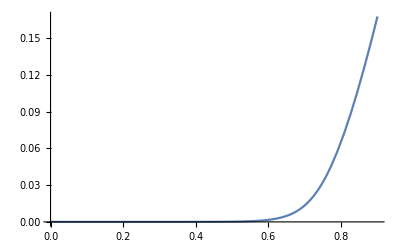

```mathematica
Id[v_,t_]:=-2.52*^-9+0.0002621830985915493 t ProductLog[(9.6116035455278*^-6 ⅇ^((9.611603545527798*^-6)/t+(6715.0147730325 v)/t))/t];
Plot[Id[v,300],{v,0,0.9},PlotRange->All]
```